Plots

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
f[r_, M_, Q_, Ns_, β_, Λ_] := 1+Q^2/r^2-(2 M)/r+Ns r^((4 β)/(1-2 β))+(r^2 Λ)/(-3+12 β)
```

## Set 01: Plot with different Q value

```mathematica
p=Plot[{f[r,1,0.6,0.01,0.02,0.02],f[r,1,0.7,0.01,0.02,0.02],f[r,1,0.8,0.01,0.02,0.02],f[r,1,0.9,0.01,0.02,0.02]},{r,0,10},PlotRange->{{0,10},{-2,2}}, PlotStyle->{Red, Black, Green, Blue}, LabelStyle->Directive[Black,Bold,15],LabelStyle->Directive[Black,Bold,15],RotateLabel->False,FrameStyle->Directive[Black,Thickness[0.002]],GridLinesStyle->Directive[Black,Thickness[0.008]],LabelStyle->Directive[Black,Bold,15],PlotTheme->"Web", RotateLabel->False,Frame->True,ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{All,Automatic},{All,Automatic}},LabelStyle->Directive[Black,20],AspectRatio->0.85,GridLinesStyle->Directive[Black,Thickness[0.003]],Frame->True,Axes->True,FrameLabel->{"r","f(r)"}, PlotLegends->Placed[{"Q = 0.6","Q = 0.7","Q = 0.8","Q = 0.9"},{0.25,0.75}]]
```

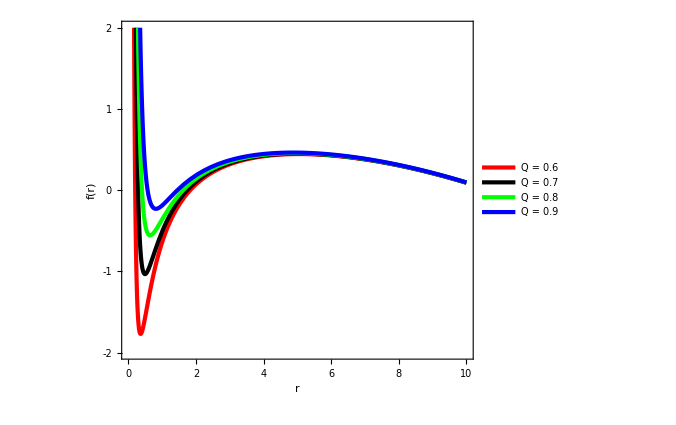

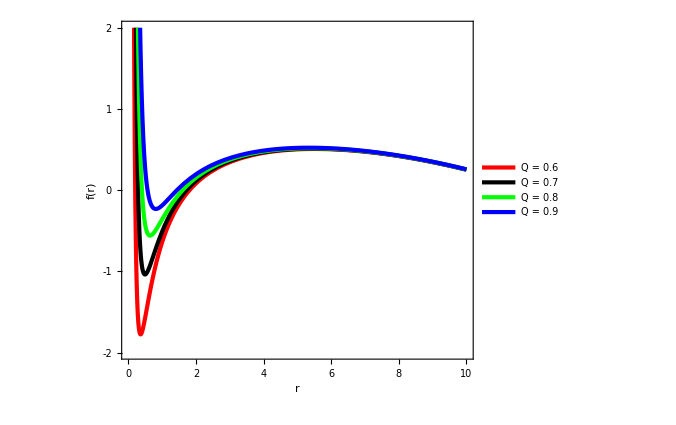

```mathematica
Export["metric_set01.pdf",%,"PDF"]
```

metric_set01.pdf

## Set 02: Plot with different Ns value (f[r, M, Q, Ns, β, Λ])

```mathematica
p=Plot[{f[r,1,0.7,0.01,0.02,0.02],f[r,1,0.7,0.03,0.02,0.02],f[r,1,0.7,0.05,0.02,0.02],f[r,1,0.7,0.07,0.02,0.02]},{r,0,10},PlotRange->{{0,10},{-2,2}}, PlotStyle->{Red, Black, Green, Blue}, LabelStyle->Directive[Black,Bold,15],LabelStyle->Directive[Black,Bold,15],RotateLabel->False,FrameStyle->Directive[Black,Thickness[0.002]],GridLinesStyle->Directive[Black,Thickness[0.008]],LabelStyle->Directive[Black,Bold,15],PlotTheme->"Web", RotateLabel->False,Frame->True,ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{All,Automatic},{All,Automatic}},LabelStyle->Directive[Black,20],AspectRatio->0.85,GridLinesStyle->Directive[Black,Thickness[0.003]],Frame->True,Axes->True,FrameLabel->{"r","f(r)"}, PlotLegends->Placed[{"N_s = 0.01","N_s = 0.03","N_s = 0.05","N_s = 0.07"},{0.25,0.75}]]
```

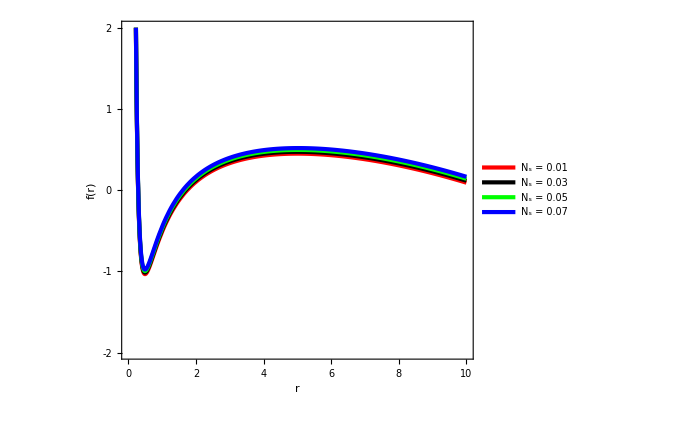

```mathematica
Export["metric_set02.pdf",%,"PDF"]
```

metric_set02.pdf

## Set 03: Plot with different β value (f[r, M, Q, Ns, β, Λ])

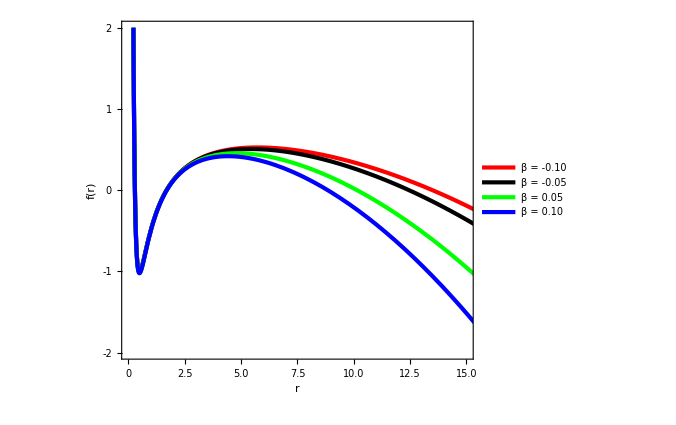

```mathematica
p=Plot[{f[r,1,0.7,0.03,-0.1,0.02],f[r,1,0.7,0.03,-0.05,0.02],f[r,1,0.7,0.03,0.05,0.02],f[r,1,0.7,0.03,0.1,0.02]},{r,0,20},PlotRange->{{0,15},{-2,2}}, PlotStyle->{Red, Black, Green, Blue}, LabelStyle->Directive[Black,Bold,15],LabelStyle->Directive[Black,Bold,15],RotateLabel->False,FrameStyle->Directive[Black,Thickness[0.002]],GridLinesStyle->Directive[Black,Thickness[0.008]],LabelStyle->Directive[Black,Bold,15],PlotTheme->"Web", RotateLabel->False,Frame->True,ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{All,Automatic},{All,Automatic}},LabelStyle->Directive[Black,20],AspectRatio->0.85,GridLinesStyle->Directive[Black,Thickness[0.003]],Frame->True,Axes->True,FrameLabel->{"r","f(r)"}, PlotLegends->Placed[{"β = -0.10","β = -0.05","β =  0.05","β =  0.10"},{0.3,0.25}]]
```

```mathematica
Export["metric_set03.pdf",%,"PDF"]
```

metric_set03.pdf

## Set 04: Plot with different Λ value (f[r, M, Q, Ns, β, Λ])

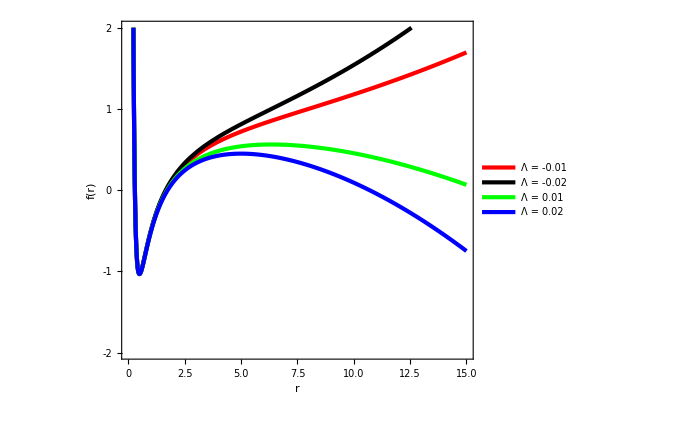

```mathematica
p=Plot[{f[r,1,0.7,0.01,0.02,-0.01],f[r,1,0.7,0.01,0.02,-0.02],f[r,1,0.7,0.01,0.02,0.01],f[r,1,0.7,0.01,0.02,0.02]},{r,0,15},PlotRange->{{0,15},{-2,2}}, PlotStyle->{Red, Black, Green, Blue}, LabelStyle->Directive[Black,Bold,15],LabelStyle->Directive[Black,Bold,15],RotateLabel->False,FrameStyle->Directive[Black,Thickness[0.002]],GridLinesStyle->Directive[Black,Thickness[0.008]],LabelStyle->Directive[Black,Bold,15],PlotTheme->"Web", RotateLabel->False,Frame->True,ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{All,Automatic},{All,Automatic}},LabelStyle->Directive[Black,20],AspectRatio->0.85,GridLinesStyle->Directive[Black,Thickness[0.003]],Frame->True,Axes->True,FrameLabel->{"r","f(r)"}, PlotLegends->Placed[{"Λ = -0.01","Λ = -0.02","Λ = 0.01","Λ = 0.02"},{0.25,0.25}]]
```

```mathematica
Export["metric_set04.pdf",%,"PDF"]
```

metric_set04.pdf